# Probability Distributions of Continuous Random Variables

In this lesson, we study the probability distribution of continuous random variables and use it to find the probability of events of interest.

## Continuous Probability Distribution

We learned that discrete random variables are things we count, while continuous random variables are things we measure.

Often we can have a subject matter for which we can collect data that could involve a discrete or a continuous random variable, depending on the information we wish to know.

Example: Classify each of the random variables described as either discrete or continuous.

The time it takes to run a mile.

The student’s height.

The number of courses the student takes this semester.

The number of siblings the student has.

The (exact) time the student spends doing school work during a week.

```mathematica
associaToGrid[data_]:=
{Join[{"x"},Part[Transpose[List@@@Normal@KeySort@(Counts@data)],1]],Join[{"P(x)"},Part[Transpose[List@@@Normal@KeySort@(Counts@data)],2]/Length[data]//N]}
```

```mathematica
(*data={Table[0,135],Table[1,271],Table[2,271],Table[3,180],Table[4,90],Table[5,36],Table[6,12],Table[7,3],Table[8,2]};
data=Flatten[data];*)
```

In previous lessons we learned that probability distributions for discrete random variables can be visualized with histograms. Each value of a discrete variable has a probability, and this probability is the area of a corresponding bar on a probability histogram.

Histogram of 5000 men’s heights.

```mathematica
data=RandomVariate[NormalDistribution[69,2.5],5000];
```

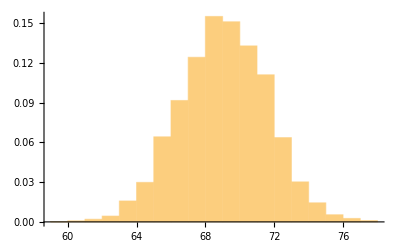

```mathematica
Histogram[data,Automatic,"Probability"]
```

We can estimate the probability of a man being between 71 and 73 inches tall by finding the area of the corresponding bar.

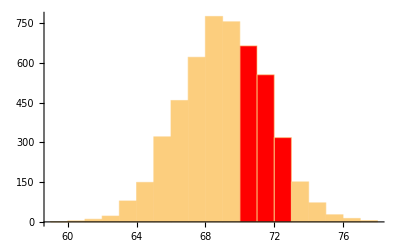

```mathematica
cedF[{{xmin_,xmax_},{ymin_,ymax_}},___]:={If[71<=xmax≤73,RGBColor[1,0,0],Sequence[]],Rectangle[{xmin,ymin},{xmax,ymax},RoundingRadius->1]};
Histogram[data,ChartElementFunction->cedF,Axes->{True,False}]
```

The problem with using a histogram is that it only allows us to estimate probabilities for a predetermined range of values. To allow more flexibility in the types of probabilities we can estimate (such as between 70.5 and 72.5 inches), it makes sense to use thinner bars.

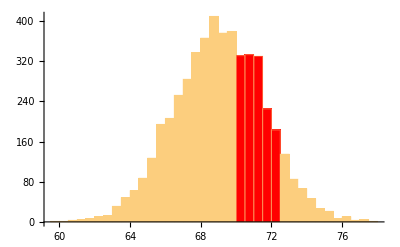

```mathematica
cedF[{{xmin_,xmax_},{ymin_,ymax_}},___]:={If[70.5<=xmax≤72.5,RGBColor[1,0,0],Sequence[]],Rectangle[{xmin,ymin},{xmax,ymax},RoundingRadius->1]};
Histogram[data,{0.5},ChartElementFunction->cedF,Axes->{True,False}]
```

Note that the outline of the histogram can be approximated nicely by a smooth curve.

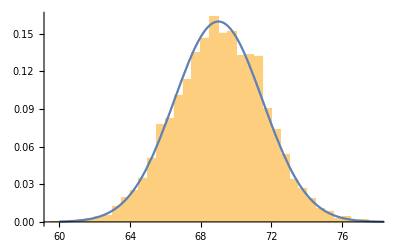

```mathematica
Show[Histogram[data,{0.5},"PDF"],Plot[PDF[NormalDistribution[69,2.5],x],{x,60,80}],Axes->{True,False}]
```

With extremely thin bars, it makes sense to use a smooth curve to model the heights of the bars. Areas under such curves represent probabilities. The total area under a probability curve is 1.

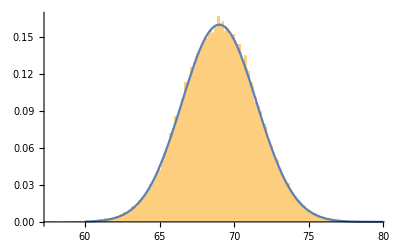

```mathematica
Show[Histogram[RandomVariate[NormalDistribution[69,2.5],100000],{0.1},"PDF"],Plot[PDF[NormalDistribution[69,2.5],x],{x,60,80}],Axes->{True,False}]
```

With a continuous curve, we can use mathematical formulas to find any area under the curve. The area represents probability. The distribution of probabilities under the curve forms a continuous probability distribution.

Below, we have shaded a region under the probability curve that extends from 67.2 to 74.3.

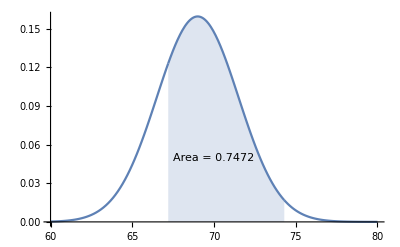

```mathematica
dist=PDF[NormalDistribution[69,2.5],#]&;
p1=Plot[dist@x,{x,60,67.2},Filling->None,PlotRange->{{60,80},All},Axes->{True,False}];
p2=Plot[dist@x,{x,67.2,74.3},Filling->Axis,PlotRange->{{60,80},{0,1}},Axes->{True,False}];
p3=Plot[dist@x,{x,74.3,80},Filling->None,PlotRange->{{60,80},All},Axes->{True,False}];
Show[p1,p2,p3,Epilog->{ Text["Area = 0.7472",{70,0.05}]}]
```

### Area and Probability

Suppose the Charles River is stocked with two types of fish, bream and bass. Below is the continuous probability distribution of fish weights in the river.

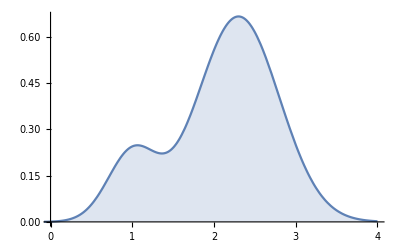

```mathematica
𝒟=MixtureDistribution[{1,5},{NormalDistribution[1,.3],NormalDistribution[2.3,.5]}];
ycor=PDF[𝒟,Table[i/2,{i,1,7}]];
area=Table[NumberForm[Probability[i/2≤x≤(i+1)/2,x\[Distributed]𝒟],1],{i,0,7}];
Plot[PDF[𝒟,x],{x,-3,4},Filling->Axis,Axes->{True,False},PlotRange->{{0,4},All}]
```

Note that the distribution starts at zero. Though the probability curve goes on and on, it is almost equal to zero for fish weights above 4 pounds.

Using the probability distribution, we can calculate probability such as a random fish weighs between 1.3 and 2.6 pounds.

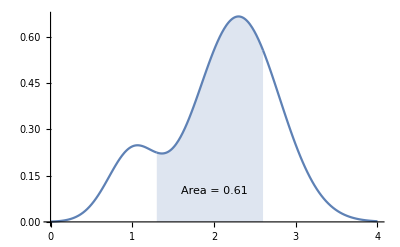

```mathematica
dist2=PDF[𝒟,#]&;
p1=Plot[dist2@x,{x,0,1.3},Filling->None,PlotRange->{{0,4},All},Axes->{True,False}];
p2=Plot[dist2@x,{x,1.3,2.6},Filling->Axis,PlotRange->{{0,4},{0,1}},Axes->{True,False}];
p3=Plot[dist2@x,{x,2.6,4},Filling->None,PlotRange->{{0,4},All},Axes->{True,False}];
Show[p1,p2,p3,Epilog->{ Text["Area = 0.61",{2,0.1}]}]
NumberForm[Probability[1.3≤x≤2.6,x\[Distributed]𝒟],4];
```

Below, the probability distribution of fish weights is divided into evenly spaced intervals. The areas of these intervals are plotted under the curve.

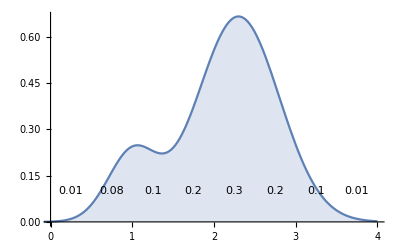

```mathematica
dplot=Plot[PDF[𝒟,x],{x,-3,4},Filling->Axis,Axes->{True,False},PlotRange->{{0,4},All},GridLines->{Table[i/2,{i,1,7}], None}];
l=1/10;
Show[dplot,Graphics[{Text[.01,{1/4,l}],Text[.08,{3/4,l}],Text[.1,{5/4,l}],Text[.2,{7/4,l}],
Text[.3,{9/4,l}],Text[.2,{11/4,l}],Text[.1,{13/4,l}],Text[.01,{15/4,l}]}]]
```

Compute the total area under the curve above. Explain why your total is the only possible answer.

Shade the region that represents the probability that a random fish weighs from 0.5 to 1.5 pounds.

```mathematica
Plot[PDF[𝒟,x],{x,-3,4},Filling->Axis,Axes->{True,False},PlotRange->{{0,4},All},GridLines->{Table[i/2,{i,1,7}], Table[i/8,{i,1,7}]}]
```

-Graphics-

Now we will let x represent the weight of a randomly selected fish. The area of the region you shaded can be written as P(0.5 ≤ x ≤ 1.5). What is this probability?

Shade the region representing the probability that the weight of a random fish is greater than or equal to 3.0 lbs.

The area of the region you shaded above is expressed as P(x ≥ 3.0). What is this probability?

## Exercises

Two thousand students took an exam (100 points total). The scores on the exam have the following distribution.

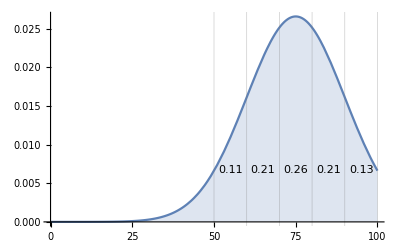

```mathematica
dist3=NormalDistribution[75,15];
dplot2=Plot[PDF[dist3,x],{x,0,100},Filling->Axis,Axes->{True,False},PlotRange->{{0,100},All},GridLines->{Table[10*i,{i,5,10}], None}];
area=Table[NumberForm[Probability[10*i≤x≤10*(i+1),x\[Distributed]dist3],1],{i,5,9}];
l=1/150;
Show[dplot2,Graphics[{Text[.11,{55,l}],Text[.21,{65,l}],Text[.26,{75,l}],Text[.21,{85,l}],
Text[.13,{95,l}]}]]
```

What is the area below 50 points?

Shade the region that represents the probability that a random student scores between 70 to 90 points. Find this probability.

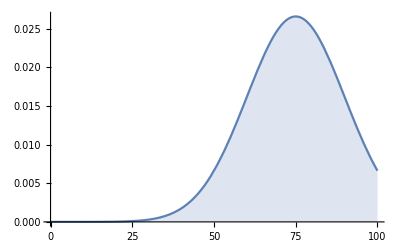

```mathematica
Plot[PDF[dist3,x],{x,0,100},Filling->Axis,Axes->{True,False},PlotRange->{{0,100},All},GridLines->{Table[10*i,{i,5,10}],Table[i/150,{i,1,3}]}]
```

Shade the region that represents the probability that a random student scores below 70 points. Find this probability.

Shade the region that represents the probability that a random student scores above 80 points. Find this probability.

## Further Exploration

```mathematica
Manipulate[
{z1,z2}=Which[zone<ztwo,{zone,ztwo},zone>ztwo,{ztwo,zone},True,{zone-eps/1000,zone+eps/1000}];
g1=If[complement,
{},
Plot[PDF[d,x],{x,-zlim,z1},Axes->False,Frame->True,PlotStyle->{Black,Thickness[Medium]},Filling->Axis,FillingStyle->RGBColor[.48,.11,.56]]];
g2=If[complement,
Plot[PDF[d,x],{x,z1,z2},Axes->False,Frame->True,PlotStyle->{Black,Thickness[Medium]},Filling->0,FillingStyle->RGBColor[.48,.11,.56]],
Plot[PDF[d,x],{x,z2,zlim},Axes->False,Frame->True,PlotStyle->{Black,Thickness[Medium]},Filling->Axis,FillingStyle->RGBColor[.48,.11,.56]]];
g3=If[complement,Plot[PDF[d,x],{x,-zlim,zlim},Axes->False,Frame->True,PlotStyle->{Black,Thickness[Medium]}],
Plot[PDF[d,x],{x,-zlim,zlim},Axes->False,Frame->True,PlotStyle->{Black,Thickness[Medium]}]];area=N[With[{a=CDF[d,z1]+(1-CDF[d,z2])},If[complement,1-a,a]]];
area=If[area≥ 0.0001,NumberForm[area,{6,4}],ScientificForm[area,4]];
Show[{g1,g2,g3},PlotRange->All,PlotLabel->Row[{"Area = ",area}],
ImageSize->{500,300}],
{{zone,-0.67,Subscript["z",1]},-4.5,4.5,0.01,Appearance->"Labeled"},{{ztwo,4.5,Subscript["z",2]},-4.5,4.5,0.01,Appearance->"Labeled"},
{{complement,False},{False,True}},
TrackedSymbols:>{zone,ztwo,complement},
Initialization:>(
zlim0=4.5;
eps=0.01;
zlim=zlim0+eps;
d=NormalDistribution[0,1];)]
```

References

I. McLeod, “Standard Normal Distribution Areas”.  http://demonstrations.wolfram.com/StandardNormalDistributionAreas/

Authorship information

Jie Frye

June 30, 2017

jiefrye@gmail.com